```mathematica
monospacedFonts=
{"Anonymous Pro","Consolas","Courier","DejaVuSansMono","DroidSansMono","Envy Code R","Inconsolata","Liberation Mono","Monaco","monofur","Panic Sans","ProFontWindows","ProggyCleanTT","Terminus"};
```

```mathematica
codingCharacters=Join[
CharacterRange["A","Z"],
CharacterRange["a","z"],
CharacterRange["0","9"],
Characters["(){}[],.:;-+*/\\&_^%$#@!~`'\"<>?"]];
```

```mathematica
CompareFontsSingleCharacter[{f1_,f2_},char_]:=
Graphics[
{Opacity@0.5,
{Red,Text[Style[char,48,FontFamily->f1]]},
{Blue,Text[Style[char,48,FontFamily->f2]]}},
ImageSize->56];
```

```mathematica
CompareFontPair[{f1_,f2_}]:=
Column[{
Graphics[{Red,Text[Style[f1,24,FontFamily->f1]]},ImageSize->{300,24}],
Graphics[{Blue,Text[Style[f2,24,FontFamily->f2]]},ImageSize->{300,24}],
GraphicsGrid@Partition[
CompareFontsSingleCharacter[{f1,f2},#]&/@codingCharacters,
13]
},Center]
```

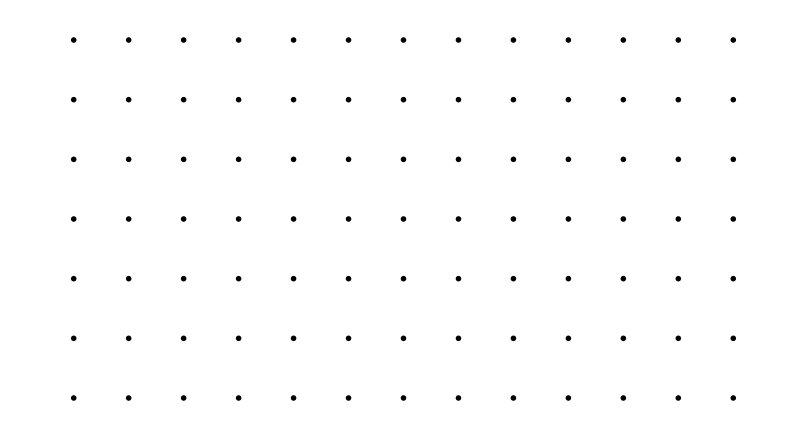
-Graphics-
-Graphics-
-Graphics-

```mathematica
CompareFontPair[{"DejaVuSansMono","DroidSansMono"}]
```

```mathematica
CompareFontPair/@Take[Subsets[monospacedFonts,{2}],4]
```

{-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-}

```mathematica
Export[
"paircompare/"<>StringReplace[StringJoin@#," "->""]<>".png",
CompareFontPair@#]&/@Subsets[monospacedFonts,{2}]
```

{paircompare/AnonymousProConsolas.png,paircompare/AnonymousProCourier.png,paircompare/AnonymousProDejaVuSansMono.png,paircompare/AnonymousProDroidSansMono.png,paircompare/AnonymousProEnvyCodeR.png,paircompare/AnonymousProInconsolata.png,paircompare/AnonymousProLiberationMono.png,paircompare/AnonymousProMonaco.png,paircompare/AnonymousPromonofur.png,paircompare/AnonymousProPanicSans.png,paircompare/AnonymousProProFontWindows.png,paircompare/AnonymousProProggyCleanTT.png,paircompare/AnonymousProTerminus.png,paircompare/ConsolasCourier.png,paircompare/ConsolasDejaVuSansMono.png,paircompare/ConsolasDroidSansMono.png,paircompare/ConsolasEnvyCodeR.png,paircompare/ConsolasInconsolata.png,paircompare/ConsolasLiberationMono.png,paircompare/ConsolasMonaco.png,paircompare/Consolasmonofur.png,paircompare/ConsolasPanicSans.png,paircompare/ConsolasProFontWindows.png,paircompare/ConsolasProggyCleanTT.png,paircompare/ConsolasTerminus.png,paircompare/CourierDejaVuSansMono.png,paircompare/CourierDroidSansMono.png,paircompare/CourierEnvyCodeR.png,paircompare/CourierInconsolata.png,paircompare/CourierLiberationMono.png,paircompare/CourierMonaco.png,paircompare/Couriermonofur.png,paircompare/CourierPanicSans.png,paircompare/CourierProFontWindows.png,paircompare/CourierProggyCleanTT.png,paircompare/CourierTerminus.png,paircompare/DejaVuSansMonoDroidSansMono.png,paircompare/DejaVuSansMonoEnvyCodeR.png,paircompare/DejaVuSansMonoInconsolata.png,paircompare/DejaVuSansMonoLiberationMono.png,paircompare/DejaVuSansMonoMonaco.png,paircompare/DejaVuSansMonomonofur.png,paircompare/DejaVuSansMonoPanicSans.png,paircompare/DejaVuSansMonoProFontWindows.png,paircompare/DejaVuSansMonoProggyCleanTT.png,paircompare/DejaVuSansMonoTerminus.png,paircompare/DroidSansMonoEnvyCodeR.png,paircompare/DroidSansMonoInconsolata.png,paircompare/DroidSansMonoLiberationMono.png,paircompare/DroidSansMonoMonaco.png,paircompare/DroidSansMonomonofur.png,paircompare/DroidSansMonoPanicSans.png,paircompare/DroidSansMonoProFontWindows.png,paircompare/DroidSansMonoProggyCleanTT.png,paircompare/DroidSansMonoTerminus.png,paircompare/EnvyCodeRInconsolata.png,paircompare/EnvyCodeRLiberationMono.png,paircompare/EnvyCodeRMonaco.png,paircompare/EnvyCodeRmonofur.png,paircompare/EnvyCodeRPanicSans.png,paircompare/EnvyCodeRProFontWindows.png,paircompare/EnvyCodeRProggyCleanTT.png,paircompare/EnvyCodeRTerminus.png,paircompare/InconsolataLiberationMono.png,paircompare/InconsolataMonaco.png,paircompare/Inconsolatamonofur.png,paircompare/InconsolataPanicSans.png,paircompare/InconsolataProFontWindows.png,paircompare/InconsolataProggyCleanTT.png,paircompare/InconsolataTerminus.png,paircompare/LiberationMonoMonaco.png,paircompare/LiberationMonomonofur.png,paircompare/LiberationMonoPanicSans.png,paircompare/LiberationMonoProFontWindows.png,paircompare/LiberationMonoProggyCleanTT.png,paircompare/LiberationMonoTerminus.png,paircompare/Monacomonofur.png,paircompare/MonacoPanicSans.png,paircompare/MonacoProFontWindows.png,paircompare/MonacoProggyCleanTT.png,paircompare/MonacoTerminus.png,paircompare/monofurPanicSans.png,paircompare/monofurProFontWindows.png,paircompare/monofurProggyCleanTT.png,paircompare/monofurTerminus.png,paircompare/PanicSansProFontWindows.png,paircompare/PanicSansProggyCleanTT.png,paircompare/PanicSansTerminus.png,paircompare/ProFontWindowsProggyCleanTT.png,paircompare/ProFontWindowsTerminus.png,paircompare/ProggyCleanTTTerminus.png}